```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
results256=Take[Import["256_results.txt", "Table"], {40,90}];
```

```mathematica
results128=Take[Import["128_results.txt", "Table"],{40,90}];
```

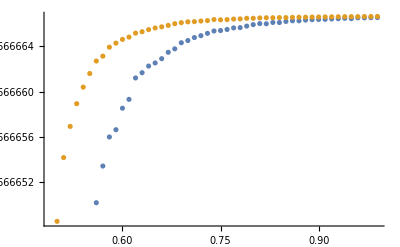

```mathematica
ListPlot[{results128,results256}]
```